```mathematica
Plot Call and Put options prices versus T-t
By Le Chen.
Crated on Mon 18 Oct 2021 10:14:47 PM CDT
```

```mathematica
∫_(-∞)^d 1/(√(2π))Exp[-x^2/2]  ⅆ x
```

1/2 (1+Erf[d/(√2)])

```mathematica
n[d_]:=1/2 (1+Erf[d/(√2)])
d1 =(Log[S/K]+(r-δ+1/2 σ^2) (T-t))/(σ √(T-t));
d2 =d1 - σ √(T-t) ;
OptionCall = S ⅇ^(-δ (T-t))n[d1] - K  ⅇ^(-r (T-t))n[d2];
OptionPut = K  ⅇ^(-r (T-t))n[-d2] - S ⅇ^(-δ (T-t))n[-d1];
```

```mathematica
Plot3D[OptionCall/.{r-> 0.08,δ->0.04,K->40,σ->0.30,T->2},{S,0,80},{t,0,1.99}]
```

-Graphics3D-

General::munfl: Exp[-1074.49] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1064.4] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-14188.6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

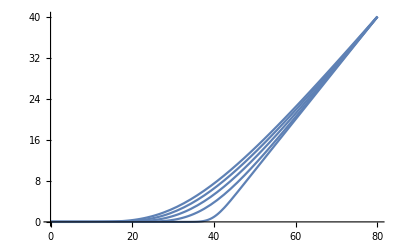

```mathematica
Plot[Table[OptionCall/.{r-> 0.08,δ->0.04,K->40,σ->0.30,T->2},{t,0,1.99,0.49}],{S,0,80}]
```

General::munfl: Exp[-1074.49] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1064.4] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-14188.6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

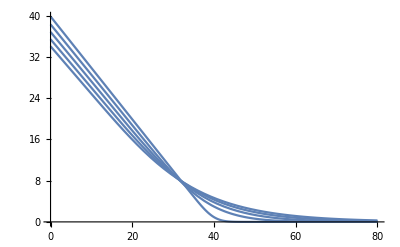

```mathematica
Plot[Table[OptionPut/.{r-> 0.08,δ->0.04,K->40,σ->0.30,T->2},{t,0,1.99,0.49}],{S,0,80}]
```